# Homework 10

Name: Muhammad Salah Shatla

ID: 201500059

Please, the code will run but it may take a relatively long time so, would you be patient while running it

## Problem 1

```mathematica
Quiet[Block[{plot2,plot3,plot4,plot5,plotList[[1]],plotList[[2]]},ClearAll["Global`*"]]]; 

dx=0.01; l=1; xList=Range[0,l,dx]; 
tmax=0.1; c=300; dt=dx/c; tList=Range[0,tmax,dt];
lt=Length[tList];
lx=Length[xList];

y=Table[0,{i,lt},{j,lx}];(*To creat a matrix*)

y0[α_,κ_,β_]=E^(-κ*(α-β)^2); (*The gaussian*)

r=1; k=1000; x0=0.55*l;(*the starting position as a fraction of the total Length*)

(*To initialize the first row of the y matrix*)
yStart=0*xList;
For[j=2,j<lx,j++,
yStart[[j]]=y0[xList[[j]],k,x0];
]

(*using the guassian as our initial Conditions*)

For[i=1,i≤2,i++,
	For[
	j=1,j≤lx,j++,
	y[[i,j]]=yStart[[j]];
	];
]

(*I made an iteration for the rest of the rows*)

For[
n=2,n<lt,n++,

	For[
	i=2,i<lx,i++,
	y[[n+1,i]]=2*(1-r^2)*y[[n,i]]-y[[n-1,i]]+r^2*(y[[n,i+1]]+y[[n,i-1]])
	
	];

	y[[n+1,1]]=y[[n+1,2]];
	y[[n+1,lx]]=y[[n+1,(lx-1)]]
]

st={FontColor->GrayLevel[.7]};
plot1=Table[ListPlot[Table[{xList[[i]],y[[n,i]]},{i,lx}],PlotRange->{All,{0,1.2}},Joined->True,LabelStyle->Directive[GrayLevel[0.5],Bold],Frame->True,Background->White,PlotStyle->{Thick,Red},AspectRatio->0.2,ImageSize->500],{n,lt}];


Framed[Manipulate[plot1[[n]],{n,1,lt,1,AnimationRate->10,Appearance->"Open"},FrameLabel->{Style["Gaussian wave on a string",FontSize->10]},Paneled->True,LabelStyle->Directive[15]],FrameMargins->25,RoundingRadius->20,Background->Blue,BaseStyle->st]
```

## Problem 2

```mathematica
Quiet[Block[{plot1,plot3,plot4,plot5,plotList[[1]],plotList[[2]]},ClearAll["Global`*"]]];

dx=0.01; d=1; xList=Range[0,d,dx]; 
tmax=0.1; c=300; dt=dx/c; tList=Range[0,tmax,dt];
lt=Length[tList];
lx=Length[xList];

y=Table[0,{i,lt},{j,lx}];

angles={50,20,110}*π/180; 
ar=angles[[1]];al=angles[[2]];ad=angles[[3]];
sr=(d Sin[ar])/Sin[ad];sl=(d Sin[al])/Sin[ad];
y01[x_]=(sr Sin[al])/(d-sr Cos[al])x; 
y02[x_]=(- Sin[al])/( Cos[al])x+d Tan[al];
r=1; k=1000; 

yStart=0*xList;
pluckPoint=Ceiling[(d-sr Cos[al])/dx];
For[j=2,j≤lx,j++,
If[j≤pluckPoint,yStart[[j]]=y01[xList[[j]]],yStart[[j]]=y02[xList[[j]]]];
]
For[i=1,i≤2,i++,
	For[
	j=1,j≤lx,j++,
	y[[i,j]]=yStart[[j]];
	];
]


For[
n=2,n<lt,n++,

	For[
	i=2,i<lx,i++,
	y[[n+1,i]]=2*(1-r^2)*y[[n,i]]-y[[n-1,i]]+r^2*(y[[n,i+1]]+y[[n,i-1]])
	
	];
]

st={FontColor->GrayLevel[.7]};
plot2=Table[ListPlot[Table[{xList[[i]],y[[n,i]]},{i,lx}],PlotRange->{All,{-0.5,0.5}},Joined->True,LabelStyle->Directive[GrayLevel[0.5],Bold],Frame->True,Background->White,PlotStyle->{Thick,Red},AspectRatio->0.2,ImageSize->700],{n,lt}];


Framed[Manipulate[plot2[[n]],{n,1,lt,1,AnimationRate->10,Appearance->"Open"},FrameLabel->{Style["Wave on a Guitar String",FontSize->12]},Paneled->False,LabelStyle->Directive[15]],FrameMargins->30,RoundingRadius->20,Background->White,BaseStyle->st]
```

## Problem 3

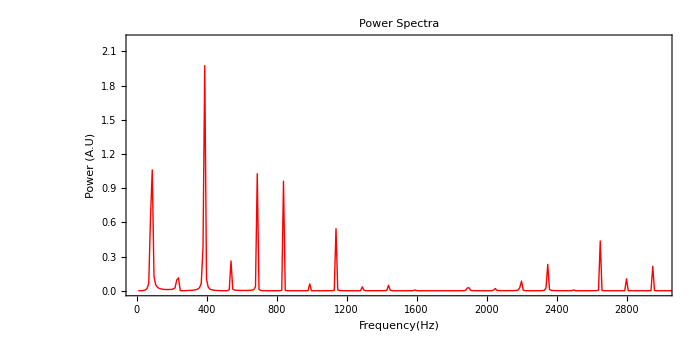

```mathematica
Quiet[Block[{plot2,plot1,plot4,plot5,plotList[[1]],plotList[[2]]},ClearAll["Global`*"]]];

dx=0.01; l=1; xList=Range[0,l,dx]; 
tmax=0.1; c=300; dt=dx/c; tList=Range[0,tmax,dt];
lt=Length[tList];
lx=Length[xList];

y=Table[0,{i,lt},{j,lx}];

y0[α_,κ_,β_]=E^(-κ*(α-β)^2); 

r=1; k=1000; x0=0.4*l; 


yStart=0*xList;
For[j=2,j<lx,j++,
yStart[[j]]=y0[xList[[j]],k,x0];
]

For[i=1,i≤2,i++,
	For[
	j=1,j≤lx,j++,
	y[[i,j]]=yStart[[j]];
	];
]

For[
n=2,n<lt,n++,

	For[
	i=2,i<lx,i++,
	y[[n+1,i]]=2*(1-r^2)*y[[n,i]]-y[[n-1,i]]+r^2*(y[[n,i+1]]+y[[n,i-1]])
	
	];
	y[[n+1,1]]=y[[n+1,2]];
]

st={FontColor->GrayLevel[.7]};
plot3=Table[ListPlot[Table[{xList[[i]],y[[n,i]]},{i,lx}],PlotRange->{All,{-1.2,1.2}},Joined->True,LabelStyle->Directive[GrayLevel[0.5],Bold],Frame->True,Background->White,PlotStyle->{Thick,Red},AspectRatio->0.2,ImageSize->700],{n,lt}];


Framed[Manipulate[plot3[[n]],{n,1,lt,1,AnimationRate->10,Appearance->"Open"},FrameLabel->{Style["Gaussian wave on a string with one free and one fixed end",FontSize->12]},Paneled->False,LabelStyle->Directive[15]],FrameMargins->30,RoundingRadius->20,Background->White,BaseStyle->st]

(*Fourier Transform*)
ft=Abs[Fourier[y[[All,Floor[(0.05*l)/dx]+1]],FourierParameters->{1,-1}]]^2;

datf=Table[{k/tmax,ft[[k]]/(3*Length[ft])},{k,1,Length[ft]}];

fPlotList=ListLinePlot[datf,PlotRange->{{0,3000},{0,2.2}},PlotLabel->"Power Spectra",LabelStyle->Directive[Green,Bold,15],
Frame->True,PlotStyle->{Thick,Red},AspectRatio->0.5,ImageSize->700];

Show[fPlotList,Frame -> True, FrameLabel->{Style["Frequency(Hz)",FontSize->15],Style["Power (A.U)",FontSize->15]}]
```

## Problem 4

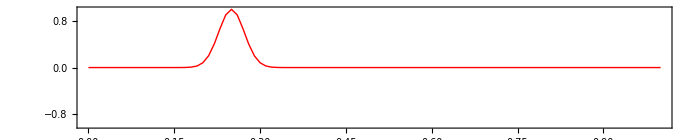

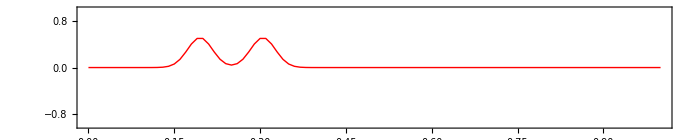

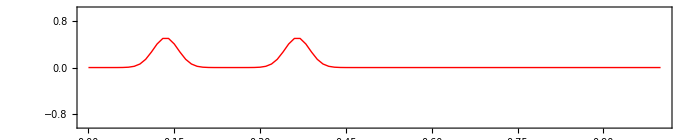

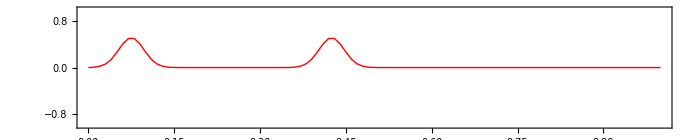

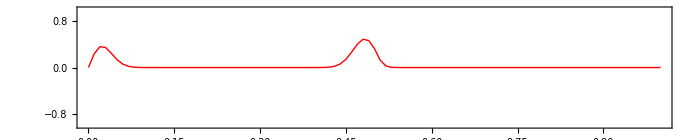

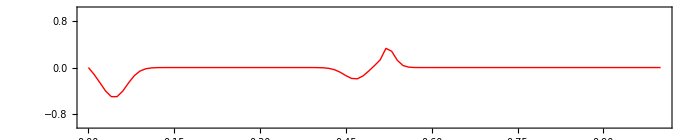

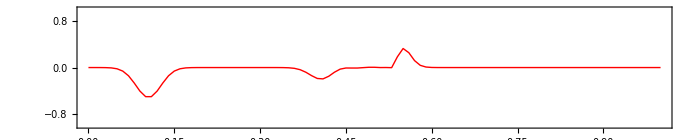

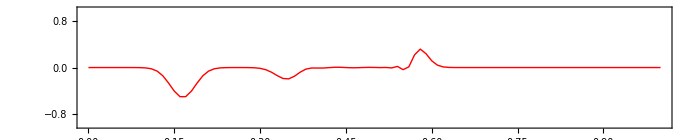

```mathematica
Quiet[Block[{plot1,plot2,plot3,plot5,plotList[[1]],plotList[[2]]},ClearAll["Global`*"]]];

dx=0.01; l=1; xList=Range[0,l,dx]; 
tmax=0.1;c=300; dt=dx/c; tList=Range[0,tmax,dt];
lt=Length[tList];
lx=Length[xList];
midPoint=Ceiling[lx/2] ;

y=Table[0,{i,lt},{j,lx}];

y0[α_,κ_,β_]=E^(-κ*(α-β)^2); (*The gaussian function*)


r={1,0.5};


 k=1000; x0=0.25*l; 


yStart=0*xList;
For[j=2,j<lx,j++,
yStart[[j]]=y0[xList[[j]],k,x0];
]
For[i=1,i≤2,i++,
	For[
	j=1,j≤lx,j++,
	y[[i,j]]=yStart[[j]];
	];
]


For[
n=2,n<lt,n++,

	For[
	i=2,i<lx,i++,



	If[i≤midPoint,y[[n+1,i]]=2*(1-r[[1]]^2)*y[[n,i]]-y[[n-1,i]]+r[[1]]^2*(y[[n,i+1]]+y[[n,i-1]]),y[[n+1,i]]=2*(1-r[[2]]^2)*y[[n,i]]-y[[n-1,i]]+r[[2]]^2*(y[[n,i+1]]+y[[n,i-1]])]	
	];
]
st={FontColor->GrayLevel[.7]};
plot4=Table[ListPlot[Table[{xList[[i]],y[[n,i]]},{i,lx}],PlotRange->{All,{-1,1}},Joined->True,LabelStyle->Directive[GrayLevel[0.5],Bold],Frame->True,Background->White,PlotStyle->{Thick,Red},AspectRatio->0.2,ImageSize->700],{n,lt}];

Framed[Manipulate[plot4[[n]],{n,1,lt,1,AnimationRate->10,Appearance->"Open"},FrameLabel->{Style["Waves on a Composite String",FontSize->12]},Paneled->False,LabelStyle->Directive[15]],FrameMargins->30,RoundingRadius->20,Background->White,BaseStyle->st]

pp=Range[1,52,6];

For[i=1,i≤Length[pp],i++,
Print[plot4[[pp[[i]]]]]
]
```

## Problem 5

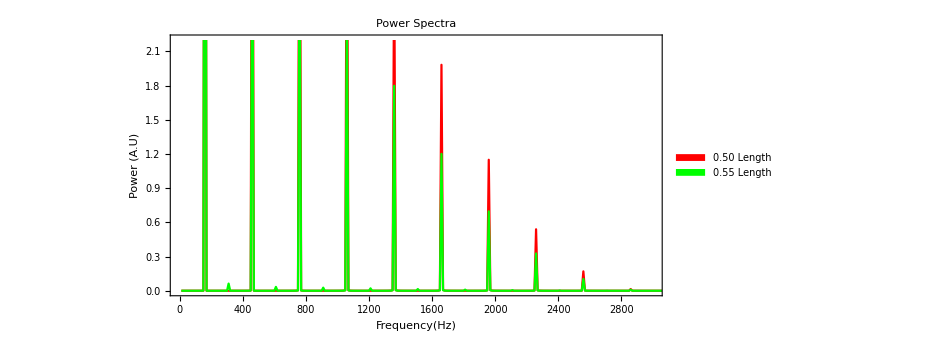

```mathematica
Quiet[Block[{plot2,plot3,plot4,plot1},ClearAll["Global`*"]]];

dx=0.01; l=1; xList=Range[0,l,dx]; 
tmax=0.1; c=300; dt=dx/c; tList=Range[0,tmax,dt];
lt=Length[tList];
lx=Length[xList];

y1=Table[0,{i,lt},{j,lx}];
y2=y1;
yList={y1,y2};
plotList=Table[0,{i,2}]; 

y0[α_,κ_,β_]=E^(-κ*(α-β)^2); 

r=1; k=1000; x0={0.5,0.55}*l;
For[k=1,k≤2,k++, 
yStart=0*xList;
For[j=2,j<lx,j++,
yStart[[j]]=y0[xList[[j]],k,x0[[k]]];
]

For[i=1,i≤2,i++,
	For[
	j=1,j≤lx,j++,
	yList[[k]][[i,j]]=yStart[[j]];
	];
]
For[
n=2,n<lt,n++,
	For[
	i=2,i<lx,i++,
	yList[[k]][[n+1,i]]=2*(1-r^2)*yList[[k]][[n,i]]-yList[[k]][[n-1,i]]+r^2*(yList[[k]][[n,i+1]]+yList[[k]][[n,i-1]])	
	];
];


st={FontColor->GrayLevel[.7]};
plot5=Table[ListPlot[Table[{xList[[i]],yList[[k]][[n,i]]},{i,lx}],PlotRange->{All,{-1.2,1.2}},Joined->True,LabelStyle->Directive[GrayLevel[0.5],Bold],Frame->True,Background->White,PlotStyle->{Thick,Red},AspectRatio->0.2,ImageSize->500],{n,lt}];
plotList[[k]]=plot5;
]

Framed[Manipulate[plotList[[1]][[n]],{n,1,lt,1,AnimationRate->10,Appearance->"Open"},FrameLabel->{Style["Gaussian wave on a string- 0.50 starting point",FontSize->12]},Paneled->False,LabelStyle->Directive[15]],FrameMargins->30,RoundingRadius->20,Background->White,BaseStyle->st]

Framed[Manipulate[plotList[[2]][[n]],{n,1,lt,1,AnimationRate->10,Appearance->"Open"},FrameLabel->{Style["Gaussian wave on a string- 0.55 starting point",FontSize->12]},Paneled->False,LabelStyle->Directive[15]],FrameMargins->30,RoundingRadius->20,Background->White,BaseStyle->st]

col={Red,Green}; 
type={"0.50 Length","0.55 Length"}; 
fPlotList={0,0}; (*a list for the 2 plots*)
For[
q=1,q≤2,q++,ft=Abs[Fourier[yList[[q]][[All,Floor[(0.05*l)/dx]+1]],FourierParameters->{1,-1}]]^2;

datf=Table[{k/tmax,ft[[k]]/(3*Length[ft])},{k,1,Length[ft]}];

fPlotList[[q]]=ListLinePlot[datf,PlotRange->{{0,3000},{0,2.2}},PlotLabel->"Power Spectra",LabelStyle->Directive[Black,Bold,15],
Frame->True,PlotStyle->{Thick,col[[q]]},PlotLegends->SwatchLegend[{type[[q]]},LegendMarkerSize->20],AspectRatio->0.5,ImageSize->700];
]
Show[fPlotList[[1]],fPlotList[[2]],Frame -> True, FrameLabel->{Style["Frequency(Hz)",FontSize->15],Style["Power (A.U)",FontSize->15]}]
```